```mathematica
(*1*)
ClearAll;
```

```mathematica
Limit[Sum[(a/(k^2+1)),{k,1,n}],n->Infinity]//FullSimplify
```

1/2 a (-1+π Coth[π])

```mathematica
(*2*)
ClearAll;
```

```mathematica
g[x_]=Piecewise[{{1+Sin[x^2]/(x^2+1),x>0},{x^2+1,x≤0}}]
```

Piecewise[{{1+Sin[x^2]/(1+x^2), x>0}, {1+x^2, x≤0}, {0, True}}]

```mathematica
NIntegrate[g[x],{x,-1,1}]
```

2.5348

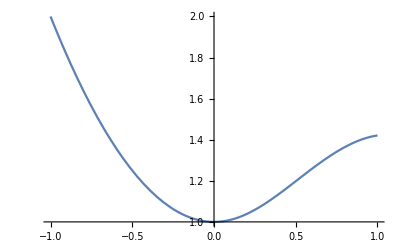

```mathematica
Plot[g[x],{x,-1,1}]
```

```mathematica
(*3*)
ClearAll;
```

```mathematica
sol1=DSolve[{D[x[t],t]==x[t]+r^2 y[t],D[y[t],t]==x[t]-y[t],x[0]==a,y[0]==0},{x[t],y[t]},t][[1]]
```

{x[t]→(a ⅇ^(-√(1+r^2) t) (-1+ⅇ^(2 √(1+r^2) t)+√(1+r^2)+ⅇ^(2 √(1+r^2) t) √(1+r^2)))/(2 √(1+r^2)),y[t]→(a ⅇ^(-√(1+r^2) t) (-1+ⅇ^(2 √(1+r^2) t)))/(2 √(1+r^2))}

```mathematica
x1[t_]=FullSimplify[x[t]/.sol1]
```

a (Cosh[√(1+r^2) t]+Sinh[√(1+r^2) t]/(√(1+r^2)))

```mathematica
y1[t_]=FullSimplify[y[t]/.sol1]
```

(a Sinh[√(1+r^2) t])/(√(1+r^2))

```mathematica
(*4*)
```

```mathematica
j[t_,r_]=FullSimplify[x1[t]/y1[t]]
```

1+√(1+r^2) Coth[√(1+r^2) t]

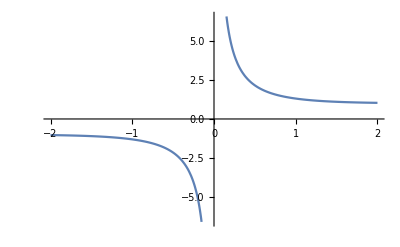

```mathematica
Plot[Coth[t],{t,-2,2}]
```

```mathematica
fg[r_]=Limit[j[t,r],t->0]
```

Indeterminate

```mathematica
fgl[r_]=Limit[j[t,r],t->-0.000001]
```

1-√(1+r^2) Coth[1.×10^-6 √(1+r^2)]

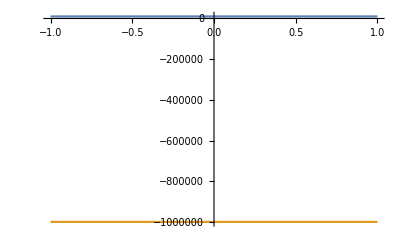

```mathematica
Plot[{fg[r],fgl[r]},{r,-1,1}]
```

```mathematica
(*5*)
ClearAll;
```

```mathematica
eq1=y''[x]+4 Sin[y[x]]-1/2y[x]^3==0
```

4 Sin[y[x]]-y[x]^3/2+y''[x]==0

```mathematica
eq2=y[0]==0
eq3=y'[0]==2.7
```

y[0]==0

y'[0]==2.7

```mathematica
NDSolve[{eq1,eq2,eq3},y[x],x]
```

NDSolve::ndlim: Range specification x is not of the form {x, xend} or {x, xmin, xmax}.

{{y[x]→InterpolatingFunction[…][x]}}

InterpolatingFunction::dmval: Input value {0.00204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

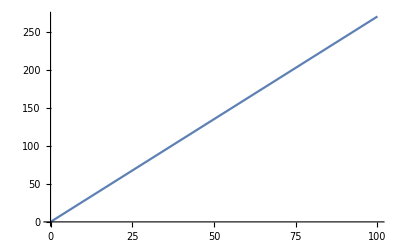

```mathematica
Plot[y[x]/.%,{x,0,100}]
```

```mathematica
(*7*)
ClearAll;
```

```mathematica
eq1=x+y+z==1
eq2=x-2 y-z-u==-1
eq3=x+3 y-z==0
eq4=x-4 y-z+u==1
```

x+y+z==1

-u+x-2 y-z==-1

x+3 y-z==0

u+x-4 y-z==1

```mathematica
Solve[{eq1,eq2,eq3,eq4},{x,y,z,u}]
```

{{x→1/2,y→0,z→1/2,u→1}}

```mathematica
(*8*)
ClearAll;
```

```mathematica
f[x_]=3/2 Cos[x]^2+x/2 -Pi
```

-π+x/2+(3 Cos[x]^2)/2

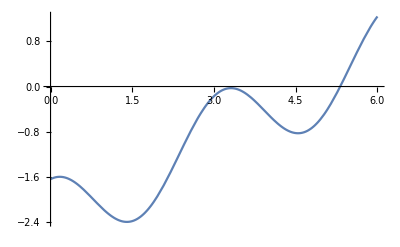

```mathematica
Plot[f[x],{x,0,6}]
```

```mathematica
FindRoot[f[x]==0,{x,3},AccuracyGoal->20]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{x→3.31151}

```mathematica
(*9*)
ClearAll;
```

```mathematica
A={0,0,1,2,1,0,2,1,2,0,1,1,2}
```

{0,0,1,2,1,0,2,1,2,0,1,1,2}

```mathematica
(*a*)
```

```mathematica
Sum[Part[A,i],{i,1,Length[A]}]
```

13

```mathematica
Sum[Part[A,i]^2,{i,1,Length[A]}]
```

21

```mathematica
B={1,0,2}
```

{1,0,2}

```mathematica
B1={1,0,1}
```

{1,0,1}

```mathematica
SubsetQ[A,B1]
```

True

```mathematica
A2=Partition[A,3,1]
```

{{0,0,1},{0,1,2},{1,2,1},{2,1,0},{1,0,2},{0,2,1},{2,1,2},{1,2,0},{2,0,1},{0,1,1},{1,1,2}}

```mathematica
MemberQ[A2,B1]
```

False